# Exercise 12

As with all of the exercises you will complete in this course, you will be expected to turn your *.nb file in to the course TA before the next lecture.  Please do so by e-mailing your completed exercise file to Lan Yu (ece329.uiuc@gmail.com), make sure you name the file using the following notation: “Exn_Last_First.nb”, where n is the Exercise number (in this case, 12), and First and Last would be your first and last name.  So my submission to Lan for this exercise would be titled “Ex12_Dan_Wasserman.nb”.  You will receive full credit for your exercise if it turned in before the next lecture (Lecture n+1).  No late submissions will be accepted.

## Objective/Overview:

In today’s exercise, we are going to investigate the relationship between current and magnetic field.  In lecture, we learned about two ways to determine the electric field from a current distribution.  The first was a brute force method, the Biot Savart Law, which allows us to determine B from an arbitrarity shaped current-carrying wire.  The second is Ampere’s Law, which is the magnetic equivalent of Gauss’s Law, and allows us to determine the B field from current distributions with certain symmetries.

```mathematica
ClearAll[dbsegment1,bzsegment1]
```

## Biot-Savart Law

In class we already determined that we can find the magnetic field from an arbitrarily-shaped current-carrying wire by integrating over all of the little elements of the wire.  
dB⃗=(μ_o I)/(4π)(ⅆ l⃗×r̂)/r^2=(μ_o I)/(4π)(ⅆ l⃗×r⃗)/r^3
This is a painstaking process, for all but the most simple of current configurations (if done by hand), but perhaps Mathematica can actually make using the Biot-Savart law a little less painful!
Let’s say we have a wire segment carrying current I, going from {0,0,0} to {1,0,0}.  Let’s calculate the magnetic field from this segment.  For now, let’s make things easy by only looking at the field in the xy plane.

```mathematica
dbsegment1=Cross[{1,0,0},{xo-x, yo,0}]/(Dot[{xo-x, yo,0},{xo-x, yo,0}])^1.5
```

{0,0,yo/(((-x+xo)^2+yo^2)^1.5)}

```mathematica
bzsegment1=Integrate[yo/(((-x+xo)^2+yo^2)^1.5),{x,0,1},Assumptions->{{x,xo,yo}∈Reals, yo≠0}]
```

yo ((1. xo)/((1.+(1. xo^2)/yo^2)^0.5 Abs[yo]^3.)+(1.-1. xo)/((1.-2. xo+1. xo^2+1. yo^2)^0.5 Abs[yo]^2.))

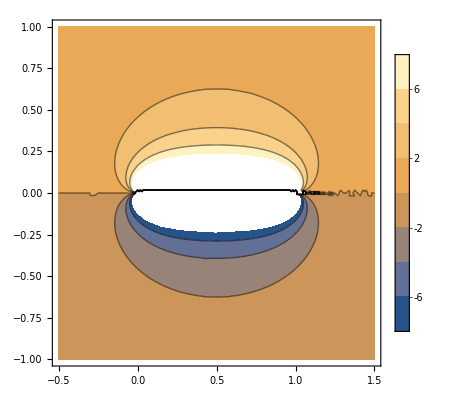

```mathematica
ContourPlot[bzsegment1,{xo,-.5,1.5},{yo,-1,1},PlotLegends->Automatic]
```

We can add another segment with current going in the -x̂ direction, from {1,1,0} to {0,1,0}

```mathematica
dbsegment2=Cross[{-1,0,0},{xo-x, yo-1,0}]/(Dot[{xo-x, yo-1,0},{xo-x, yo-1,0}])^1.5
```

{0,0,(1-yo)/(((-x+xo)^2+(-1+yo)^2)^1.5)}

```mathematica
bzsegment2=Integrate[(1-yo)/(((-x+xo)^2+(-1+yo)^2)^1.5),{x,0,1},Assumptions->{{x,xo,yo}∈Reals, yo≠1}]
```

-((-1+yo) (1.-2. yo+yo^2)^0.5 ((1. xo)/((1.+1. xo^2-2. yo+1. yo^2)^0.5)+1./((2.-2. xo+1. xo^2-2. yo+1. yo^2)^0.5)-(1. xo)/((2.-2. xo+1. xo^2-2. yo+1. yo^2)^0.5)))/Abs[-1.+yo]^3.

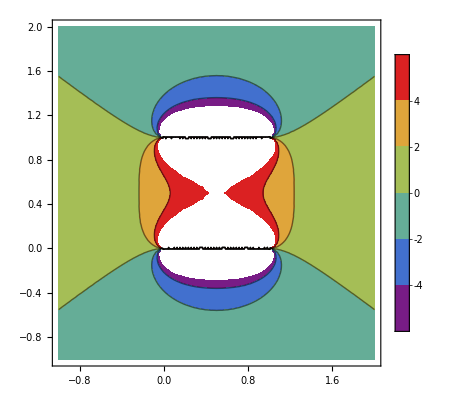

```mathematica
ContourPlot[bzsegment1+bzsegment2,{xo,-1,2},{yo,-1,2},PlotLegends->Automatic, ColorFunction->"Rainbow"]
```

We can complete the current square by adding currents in the +/- y directions at x=1 and x=0

```mathematica
dbsegment3=Cross[{0,1,0},{xo-1, yo-y,0}]/(Dot[{xo-1, yo-y,0},{xo-1, yo-y,0}])^1.5
```

{0,0,(1-xo)/(((-1+xo)^2+(-y+yo)^2)^1.5)}

```mathematica
bzsegment3=Integrate[(1-xo)/(((-1+xo)^2+(-y+yo)^2)^1.5),{y,0,1},Assumptions->{{x,xo,yo}∈Reals, xo≠1}]
```

((1-xo) (1.-2. xo+xo^2)^0.5 ((1. yo)/((1.-2. xo+1. xo^2+1. yo^2)^0.5)+1./((2.-2. xo+1. xo^2-2. yo+1. yo^2)^0.5)-(1. yo)/((2.-2. xo+1. xo^2-2. yo+1. yo^2)^0.5)))/Abs[-1.+xo]^3.

```mathematica
dbsegment4=Cross[{0,-1,0},{xo, yo-y,0}]/(Dot[{xo, yo-y,0},{xo, yo-y,0}])^1.5
```

{0,0,xo/((xo^2+(-y+yo)^2)^1.5)}

```mathematica
bzsegment4=Integrate[xo/((xo^2+(-y+yo)^2)^1.5),{y,0,1},Assumptions->{{x,xo,yo}∈Reals, xo≠0}]
```

xo ((1. yo)/((1.+(1. yo^2)/xo^2)^0.5 Abs[xo]^3.)+(1.-1. yo)/((1.+1. xo^2-2. yo+1. yo^2)^0.5 Abs[xo]^2.))

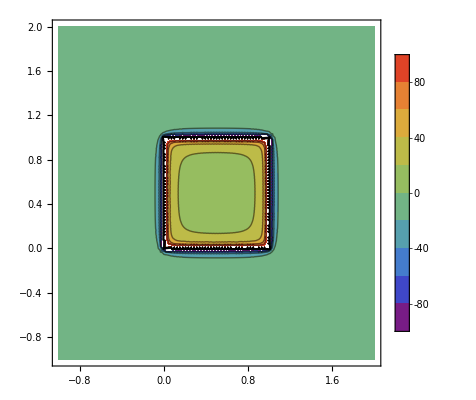

```mathematica
ContourPlot[bzsegment1+bzsegment2+bzsegment3+bzsegment4,{xo,-1,2},{yo,-1,2},PlotLegends->Automatic, ColorFunction->"Rainbow", PlotRange->100]
```

This is kind of interesting...we see that inside the loop we have basically a constant magnetic field in the z direction (except at the wires, where the field diverges), and outside of the loop we basically no magnetic field!
Use the Biot Savart Law to calculate the magnetic field from this structure along the z axis.  In other words, plot B(z) for x=y=0.  Let’s move our loop to be centered on the z-axis:

```mathematica
dbsegment1z=Cross[{1,0,0},{x, 0.5,zo}]/(Dot[{x, 0.5,zo},{x, 0.5,zo}])^1.5
```

{0.,-zo/((0.25+x^2+zo^2)^1.5),0.5/((0.25+x^2+zo^2)^1.5)}

```mathematica
bzsegment1z=Simplify[Integrate[0.5/((0.25+x^2+zo^2)^1.5),{x,-.5,.5},Assumptions->{{x,xo,zo}∈Reals}]]
```

0.5/((0.25+zo^2)^1. (0.5+1. zo^2)^0.5)

```mathematica
dbsegment2z=Cross[{0,1,0},{-.5, -y,zo}]/(Dot[{-.5, -y,zo},{-.5,-y,zo}])^1.5
```

{zo/((0.25+y^2+zo^2)^1.5),0.,0.5/((0.25+y^2+zo^2)^1.5)}

```mathematica
bzsegment2z=Simplify[Integrate[0.5/((0.25+y^2+zo^2)^1.5),{y,-.5,.5},Assumptions->{{y,xo,zo}∈Reals}]]
```

0.5/((0.25+zo^2)^1. (0.5+1. zo^2)^0.5)

```mathematica
bzall=4*0.5/((0.25+zo^2)^1. (0.5+1. zo^2)^0.5)
```

2./((0.25+zo^2)^1. (0.5+1. zo^2)^0.5)

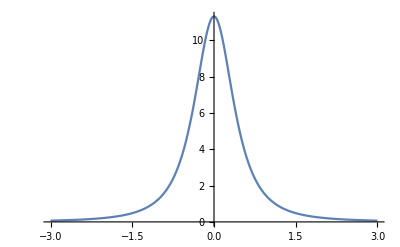

```mathematica
Plot[bzall,{zo,-3,3}]
```

Using the Biot-Savart law is computationally intensive, and oftentimes next to impossible analytically, which is why in this class, we tend to use Ampere’s Law.  Our next exercise will focus on using Ampere’s Law.  For the rest of this exercise, we will focus on the super-position principle.

## Superposition Principle with Magnetic Fields from Infinite Wires

In class we stated that the Magnetic field from an infinite wire carrying a current I was given by B⃗=(μ_o I)/(2πr)θ̂. Where θ̂ is the unit vector associated the azimuthal direction ‘curling’ around the current carrying wire.  Let’s see in we can plot this, assuming (μ_o I)/(2π)=1.

```mathematica
bwire={0,1/r}
```

{0,1/r}

```mathematica
bwirexyz=TransformedField["Polar"->"Cartesian",bwire,{r,θ}->{x,y}]
```

{-y/(x^2+y^2),x/(x^2+y^2)}

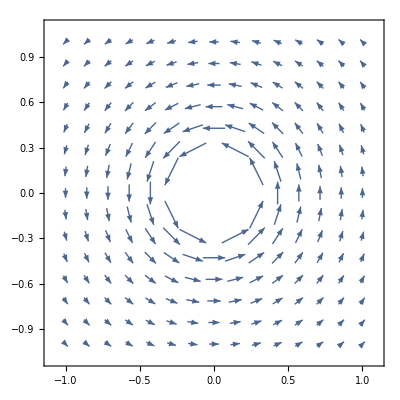

```mathematica
VectorPlot[Boole[x^2+y^2≥0.1]bwirexyz,{x,-1,1},{y,-1,1},VectorScale->Automatic]
```

Here I just excluded the region where r<0.1 from the vector plot since the magnitude of the B field diverges at r=0 and this will make the vector field very difficult to visualize.
Let’s add a second wire, carrying the same current in the same direction, at x=0.5.

```mathematica
b2wire={-y/(x^2+y^2),x/(x^2+y^2)}+{-y/((x-.5)^2+y^2),(x-.5)/((x-.5)^2+y^2)}
```

{-y/((-0.5+x)^2+y^2)-y/(x^2+y^2),(-0.5+x)/((-0.5+x)^2+y^2)+x/(x^2+y^2)}

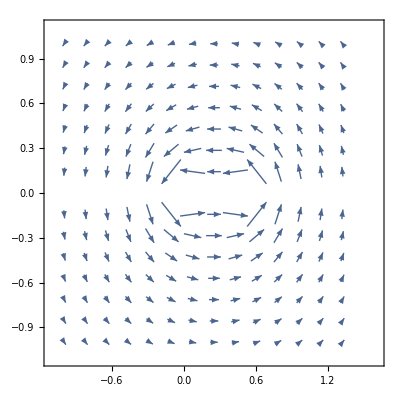

```mathematica
VectorPlot[Boole[Abs[y]≥ 0.05]b2wire,{x,-1,1.5},{y,-1,1},VectorScale->Automatic]
```

Continue adding wires, playing with the number of wires and the density of wires along the x-axis.  What do you notice about the magnetic field above and below the wires as you increase wire density and the number of wires?  It might help to plot the region above y=0 and the region below y=0, as we did above.  What you are doing here is nothing more than what we did intuitively in the lecture.  You are numerically showing that you can model a current sheet using a combination of current-carrying wires.  Plot the amplitude of the B-field (B_x(y)) as a function of y from your results:

```mathematica
btotal=Sum[{-y/((x-n*0.1)^2+y^2),(x-n*0.1)/((x-n*0.1)^2+y^2)},{n,30}]
```

{-y/((-3.+x)^2+y^2)-y/((-2.9+x)^2+y^2)-y/((-2.8+x)^2+y^2)-y/((-2.7+x)^2+y^2)-y/((-2.6+x)^2+y^2)-y/((-2.5+x)^2+y^2)-y/((-2.4+x)^2+y^2)-y/((-2.3+x)^2+y^2)-y/((-2.2+x)^2+y^2)-y/((-2.1+x)^2+y^2)-y/((-2.+x)^2+y^2)-y/((-1.9+x)^2+y^2)-y/((-1.8+x)^2+y^2)-y/((-1.7+x)^2+y^2)-y/((-1.6+x)^2+y^2)-y/((-1.5+x)^2+y^2)-y/((-1.4+x)^2+y^2)-y/((-1.3+x)^2+y^2)-y/((-1.2+x)^2+y^2)-y/((-1.1+x)^2+y^2)-y/((-1.+x)^2+y^2)-y/((-0.9+x)^2+y^2)-y/((-0.8+x)^2+y^2)-y/((-0.7+x)^2+y^2)-y/((-0.6+x)^2+y^2)-y/((-0.5+x)^2+y^2)-y/((-0.4+x)^2+y^2)-y/((-0.3+x)^2+y^2)-y/((-0.2+x)^2+y^2)-y/((-0.1+x)^2+y^2),(-3.+x)/((-3.+x)^2+y^2)+(-2.9+x)/((-2.9+x)^2+y^2)+(-2.8+x)/((-2.8+x)^2+y^2)+(-2.7+x)/((-2.7+x)^2+y^2)+(-2.6+x)/((-2.6+x)^2+y^2)+(-2.5+x)/((-2.5+x)^2+y^2)+(-2.4+x)/((-2.4+x)^2+y^2)+(-2.3+x)/((-2.3+x)^2+y^2)+(-2.2+x)/((-2.2+x)^2+y^2)+(-2.1+x)/((-2.1+x)^2+y^2)+(-2.+x)/((-2.+x)^2+y^2)+(-1.9+x)/((-1.9+x)^2+y^2)+(-1.8+x)/((-1.8+x)^2+y^2)+(-1.7+x)/((-1.7+x)^2+y^2)+(-1.6+x)/((-1.6+x)^2+y^2)+(-1.5+x)/((-1.5+x)^2+y^2)+(-1.4+x)/((-1.4+x)^2+y^2)+(-1.3+x)/((-1.3+x)^2+y^2)+(-1.2+x)/((-1.2+x)^2+y^2)+(-1.1+x)/((-1.1+x)^2+y^2)+(-1.+x)/((-1.+x)^2+y^2)+(-0.9+x)/((-0.9+x)^2+y^2)+(-0.8+x)/((-0.8+x)^2+y^2)+(-0.7+x)/((-0.7+x)^2+y^2)+(-0.6+x)/((-0.6+x)^2+y^2)+(-0.5+x)/((-0.5+x)^2+y^2)+(-0.4+x)/((-0.4+x)^2+y^2)+(-0.3+x)/((-0.3+x)^2+y^2)+(-0.2+x)/((-0.2+x)^2+y^2)+(-0.1+x)/((-0.1+x)^2+y^2)}

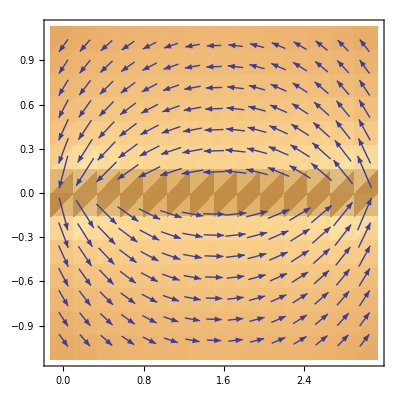

```mathematica
VectorDensityPlot[Boole[Abs[y]≥ 0.01]btotal,{x,0,3},{y,-1,1},VectorScale->Automatic]
```

```mathematica
btotalxofy[x_,y_]=btotal[[1]]
```

-y/((-3.+x)^2+y^2)-y/((-2.9+x)^2+y^2)-y/((-2.8+x)^2+y^2)-y/((-2.7+x)^2+y^2)-y/((-2.6+x)^2+y^2)-y/((-2.5+x)^2+y^2)-y/((-2.4+x)^2+y^2)-y/((-2.3+x)^2+y^2)-y/((-2.2+x)^2+y^2)-y/((-2.1+x)^2+y^2)-y/((-2.+x)^2+y^2)-y/((-1.9+x)^2+y^2)-y/((-1.8+x)^2+y^2)-y/((-1.7+x)^2+y^2)-y/((-1.6+x)^2+y^2)-y/((-1.5+x)^2+y^2)-y/((-1.4+x)^2+y^2)-y/((-1.3+x)^2+y^2)-y/((-1.2+x)^2+y^2)-y/((-1.1+x)^2+y^2)-y/((-1.+x)^2+y^2)-y/((-0.9+x)^2+y^2)-y/((-0.8+x)^2+y^2)-y/((-0.7+x)^2+y^2)-y/((-0.6+x)^2+y^2)-y/((-0.5+x)^2+y^2)-y/((-0.4+x)^2+y^2)-y/((-0.3+x)^2+y^2)-y/((-0.2+x)^2+y^2)-y/((-0.1+x)^2+y^2)

```mathematica
btotalxofy[1.5,y]
```

-y/(0.+y^2)-y/(0.01+y^2)-y/(0.01+y^2)-y/(0.04+y^2)-y/(0.04+y^2)-y/(0.09+y^2)-y/(0.09+y^2)-y/(0.16+y^2)-y/(0.16+y^2)-(2 y)/(0.25+y^2)-y/(0.36+y^2)-y/(0.36+y^2)-y/(0.49+y^2)-y/(0.49+y^2)-y/(0.64+y^2)-y/(0.64+y^2)-y/(0.81+y^2)-y/(0.81+y^2)-(2 y)/(1.+y^2)-(2 y)/(1.21+y^2)-y/(1.44+y^2)-y/(1.44+y^2)-y/(1.69+y^2)-y/(1.69+y^2)-y/(1.96+y^2)-y/(1.96+y^2)-y/(2.25+y^2)

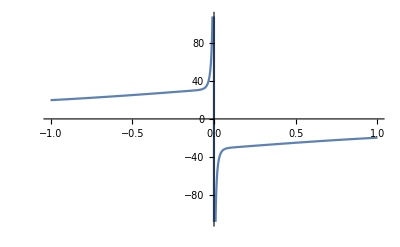

```mathematica
Plot[btotalxofy[1.5,y],{y,-1,1}]
```